# NewDsSet example

NewDsSet call is similar to NewDsBasis, but this procedure allows for  linear dependent sets (thus Basis→Set in the name) of denominators. 
Many options of NewDsBasis are valid also for NewDsSet.

HQET diagrams often contain linearly dependent denominators, so we will use HQET propagators in this example.

## Preamble

```mathematica
SetDirectory[NotebookDirectory[]]
<<Fermatica`
<<LiteRed2`
```

/home/roma/Programming/LiteRed2/LiteRed2 (public)/Examples

******************** Fermatica v1.01 ********************
Inteface to [Fermat CAS](http://home.bway.net/lewis/).
© Roman N. Lee, 2018.
Read from: /home/roma/Programming/Fermatica/Fermatica.wl (CRC32: 3494419474)

/home/roma/Programs/ferl6/fer64:
Fermat for Linux, Intel64, rational C version 6.5

**************** LiteRed v2.023β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Sat 10 Jun 2023 12:36:17
Read from:/home/roma/Programming/LiteRed2/LiteRed2 (public)/Source/LiteRed2023.m (CRC32:3671070929,{3552868898, 3930760867, 3144333369, 2439625558})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

Found "APtsort" library.

```mathematica
SetDim[d];
Declare[{p1,p2,p3,p4,p5,p6,p7,p8,l1,l2,l3,v},Vector];
sp[v]=1;n=v;
```

Thick red lines denote HQET propagators, blue lines denote massless denominators.

```mathematica
SetOptions[FeynGraphPlot,EdgeStyle->{0:>Blue,1:>{Red,Thick}}];
```

## Ds Bases

We first define graphs:

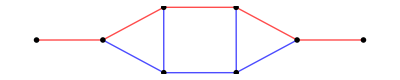
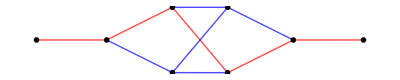
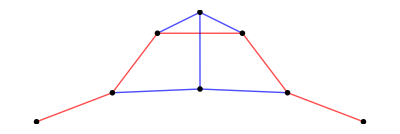
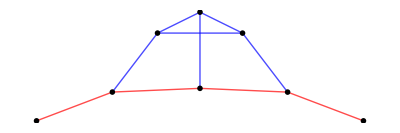

```mathematica
topos={
{{1->2,1},{2->3,1},{3->4,1},{1->5,0},{2->5,0},{5->6,0},{6->3,0},{6->4,0},{-1->1,1,0},{4->-4,1,0}},
{{1->2,1},{2->3,1},{3->4,1},{1->5,0},{3->5,0},{5->6,0},{6->2,0},{6->4,0},{-1->1,1,0},{4->-4,1,0}},
{{1->2,1},{2->3,1},{3->4,1},{1->5,0},{4->5,0},{5->6,0},{6->2,0},{6->3,0},{-1->1,1,0},{4->-4,1,0}},
{{1->2,1},{2->3,1},{1->4,0},{2->5,0},{3->6,0},{4->5,0},{5->6,0},{6->4,0},{-1->1,1,0},{3->-3,1,0}}
};Row[FeynGraphPlot/@topos]
```

GraphToDs converts graphs to denominators.

```mathematica
(dslist=GraphToDs[#,{l1,l2,l3},Switch[#1,1,1-2sp[#2,v],0,-sp[#2]]&]&/@topos)
```

{{1-2 l1·v,1-2 l2·v,1-2 l3·v,-((-l1)·(-l1)),-((l1-l2)·(l1-l2)),-((-l2)·(-l2)),-((-l2+l3)·(-l2+l3)),-((-l3)·(-l3))},{1-2 l1·v,1-2 l2·v,1-2 l3·v,-((-l1)·(-l1)),-((l2-l3)·(l2-l3)),-((-l1+l2-l3)·(-l1+l2-l3)),-((-l1+l2)·(-l1+l2)),-((-l3)·(-l3))},{1-2 l1·v,1-2 l2·v,1-2 l3·v,-((-l1)·(-l1)),-(l3·l3),-((-l1+l3)·(-l1+l3)),-((-l1+l2)·(-l1+l2)),-((-l2+l3)·(-l2+l3))},{1-2 l1·v,1-2 l2·v,-((-l1)·(-l1)),-((l1-l2)·(l1-l2)),-(l2·l2),-(l3·l3),-((l1-l2+l3)·(l1-l2+l3)),-((l1+l3)·(l1+l3))}}

Now we search for the rules.

```mathematica
NewDsBasis[HQET1,dslist[[1]],{l1,l2,l3},Append->True,SolvejSector->True,Directory->"Bases/HQET1"];
```

Irreducible numerator(s) appended: l1·l3.
Using {___, 0} as a pattern for AnalyzeSectors.

HQET1 is valid basis. The definitions of the basis will be saved in "Bases/HQET1" directory.
    Ds[HQET1] — denominators,
    SPs[HQET1] — scalar products involving loop momenta,
    LMs[HQET1] — loop momenta,
    EMs[HQET1] — external momenta,
    Parameters[HQET1] — parameters (invariants, masses, dimension),
    Toj[HQET1] — rules to transform scalar products to denominators,
    CutDs[HQET1] — flag vector of cut denominators.

The directory Bases/HQET1 has been created.

Generating IBP…

Identities are generated.
    IBP[HQET1] — integration-by-part identities,
    LI[HQET1] — Lorentz invariance identities.

Analyzing sectors…

Found 209(47) zero(nonzero) sectors out of 256.
    ZeroSectors[HQET1] — zero sectors,
    NonZeroSectors[HQET1] — nonzero sectors,
    SimpleSectors[HQET1] — simple sectors (no nonzero subsectors),
    BasisSectors[HQET1] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[HQET1] — a rule to nullify all zero j[HQET1…],
    CutDs[HQET1] — a flag list of cut denominators (1=cut).

Finding symmetries…

Found 22 mapped sectors and 25 unique sectors.
    UniqueSectors[HQET1] — unique sectors.
    MappedSectors[HQET1] — mapped sectors.
    SR[HQET1][…] — symmetry relations for j[HQET1,…] from UniqueSectors[HQET1].
    jSymmetries[HQET1,…] — symmetry rules for the sector js[HQET1,…] in UniqueSectors[HQET1].
    jRules[HQET1,…] — reduction rules for j[HQET1,…] from MappedSectors[HQET1].
    SectorsMappings[HQET1] gives the list of mappings of all sectors from MappedSectors[HQET1] to UniqueSectors[HQET1].

Solving sectors…

About to solve 25 unique sectors of HQET1 basis.

Sector js[HQET1,0,0,1,1,1,0,1,0,0]

jRules[HQET1, 0, 0, 1, 1, 1, 0, 1, 0, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 1 integrals (j[HQET1, 0, 0, 1, 1, 1, 0, 1, 0, 0]).

Sector js[HQET1,0,0,1,1,1,0,1,1,0]

jRules[HQET1, 0, 0, 1, 1, 1, 0, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,0,0,1,1,1,1,1,0,0]

jRules[HQET1, 0, 0, 1, 1, 1, 1, 1, 0, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,0,1,0,1,1,0,1,1,0]

jRules[HQET1, 0, 1, 0, 1, 1, 0, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 1 integrals (j[HQET1, 0, 1, 0, 1, 1, 0, 1, 1, 0]).

Sector js[HQET1,0,1,1,1,1,0,0,1,0]

jRules[HQET1, 0, 1, 1, 1, 1, 0, 0, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 1 integrals (j[HQET1, 0, 1, 1, 1, 1, 0, 0, 1, 0]).

Sector js[HQET1,0,1,1,1,1,0,1,0,0]

jRules[HQET1, 0, 1, 1, 1, 1, 0, 1, 0, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,1,0,1,0,1,0,1,1,0]

jRules[HQET1, 1, 0, 1, 0, 1, 0, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,1,0,1,0,1,1,1,0,0]

jRules[HQET1, 1, 0, 1, 0, 1, 1, 1, 0, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 1 integrals (j[HQET1, 1, 0, 1, 0, 1, 1, 1, 0, 0]).

Sector js[HQET1,0,0,1,1,1,1,1,1,0]

jRules[HQET1, 0, 0, 1, 1, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,0,1,0,1,1,1,1,1,0]

jRules[HQET1, 0, 1, 0, 1, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,0,1,1,1,1,0,1,1,0]

jRules[HQET1, 0, 1, 1, 1, 1, 0, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,0,1,1,1,1,1,0,1,0]

jRules[HQET1, 0, 1, 1, 1, 1, 1, 0, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,0,1,1,1,1,1,1,0,0]

jRules[HQET1, 0, 1, 1, 1, 1, 1, 1, 0, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,1,0,1,0,1,1,1,1,0]

jRules[HQET1, 1, 0, 1, 0, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,1,0,1,1,1,0,1,1,0]

jRules[HQET1, 1, 0, 1, 1, 1, 0, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 1 integrals (j[HQET1, 1, 0, 1, 1, 1, 0, 1, 1, 0]).

Sector js[HQET1,1,1,1,0,1,0,1,1,0]

jRules[HQET1, 1, 1, 1, 0, 1, 0, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,1,1,1,0,1,1,0,1,0]

jRules[HQET1, 1, 1, 1, 0, 1, 1, 0, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,1,1,1,0,1,1,1,0,0]

jRules[HQET1, 1, 1, 1, 0, 1, 1, 1, 0, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,1,1,1,1,0,1,0,1,0]

jRules[HQET1, 1, 1, 1, 1, 0, 1, 0, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 1 integrals (j[HQET1, 1, 1, 1, 1, 0, 1, 0, 1, 0]).

Sector js[HQET1,0,1,1,1,1,1,1,1,0]

jRules[HQET1, 0, 1, 1, 1, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,1,0,1,1,1,1,1,1,0]

jRules[HQET1, 1, 0, 1, 1, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,1,1,1,0,1,1,1,1,0]

jRules[HQET1, 1, 1, 1, 0, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,1,1,1,1,0,1,1,1,0]

jRules[HQET1, 1, 1, 1, 1, 0, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

Sector js[HQET1,1,1,1,1,1,0,1,1,0]

jRules[HQET1, 1, 1, 1, 1, 1, 0, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 1 integrals (j[HQET1, 1, 1, 1, 1, 1, 0, 1, 1, 0]).

Sector js[HQET1,1,1,1,1,1,1,1,1,0]

jRules[HQET1, 1, 1, 1, 1, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET1] — list of master integrals appended with 0 integrals.

```mathematica
NewDsBasis[HQET2,dslist[[2]],{l1,l2,l3},Append->True,SolvejSector->True,Directory->"Bases/HQET2",FindExtSymmetries->{HQET1}];
```

Irreducible numerator(s) appended: l1·l2.
Using {___, 0} as a pattern for AnalyzeSectors.

HQET2 is valid basis. The definitions of the basis will be saved in "Bases/HQET2" directory.
    Ds[HQET2] — denominators,
    SPs[HQET2] — scalar products involving loop momenta,
    LMs[HQET2] — loop momenta,
    EMs[HQET2] — external momenta,
    Parameters[HQET2] — parameters (invariants, masses, dimension),
    Toj[HQET2] — rules to transform scalar products to denominators,
    CutDs[HQET2] — flag vector of cut denominators.

The directory Bases/HQET2 has been created.

Generating IBP…

Identities are generated.
    IBP[HQET2] — integration-by-part identities,
    LI[HQET2] — Lorentz invariance identities.

Analyzing sectors…

Found 193(63) zero(nonzero) sectors out of 256.
    ZeroSectors[HQET2] — zero sectors,
    NonZeroSectors[HQET2] — nonzero sectors,
    SimpleSectors[HQET2] — simple sectors (no nonzero subsectors),
    BasisSectors[HQET2] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[HQET2] — a rule to nullify all zero j[HQET2…],
    CutDs[HQET2] — a flag list of cut denominators (1=cut).

Finding external symmetries…

Found 47 sectors mapped onto HQET1.
    ExtUniqueSectors[HQET2] — new sectors of the basis.
    ExtMappedSectors[HQET2] — a list of mapped sectors.
    jExtRules[HQET2,…] — reduction rules for j[HQET2,…] from ExtMappedSectors[HQET2].
    ExtSectorsMappings[HQET2] — gives the list of mappings of all sectors from ExtMappedSectors[HQET2] to unique sectors of other bases.

Finding symmetries…

Found 6 mapped sectors and 10 unique sectors.
    UniqueSectors[HQET2] — unique sectors.
    MappedSectors[HQET2] — mapped sectors.
    SR[HQET2][…] — symmetry relations for j[HQET2,…] from UniqueSectors[HQET2].
    jSymmetries[HQET2,…] — symmetry rules for the sector js[HQET2,…] in UniqueSectors[HQET2].
    jRules[HQET2,…] — reduction rules for j[HQET2,…] from MappedSectors[HQET2].
    SectorsMappings[HQET2] gives the list of mappings of all sectors from MappedSectors[HQET2] to UniqueSectors[HQET2].

Solving sectors…

About to solve 10 unique sectors of HQET2 basis.

Sector js[HQET2,0,1,0,1,1,1,1,1,0]

jRules[HQET2, 0, 1, 0, 1, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET2] — list of master integrals appended with 0 integrals.

Sector js[HQET2,0,1,1,1,1,1,0,1,0]

jRules[HQET2, 0, 1, 1, 1, 1, 1, 0, 1, 0] — reduction rules for the sector.
    MIs[HQET2] — list of master integrals appended with 0 integrals.

Sector js[HQET2,0,1,1,1,1,1,1,0,0]

jRules[HQET2, 0, 1, 1, 1, 1, 1, 1, 0, 0] — reduction rules for the sector.
    MIs[HQET2] — list of master integrals appended with 0 integrals.

Sector js[HQET2,1,1,1,0,1,1,0,1,0]

jRules[HQET2, 1, 1, 1, 0, 1, 1, 0, 1, 0] — reduction rules for the sector.
    MIs[HQET2] — list of master integrals appended with 0 integrals.

Sector js[HQET2,1,1,1,0,1,1,1,0,0]

jRules[HQET2, 1, 1, 1, 0, 1, 1, 1, 0, 0] — reduction rules for the sector.
    MIs[HQET2] — list of master integrals appended with 0 integrals.

Sector js[HQET2,1,1,1,1,0,1,0,1,0]

jRules[HQET2, 1, 1, 1, 1, 0, 1, 0, 1, 0] — reduction rules for the sector.
    MIs[HQET2] — list of master integrals appended with 1 integrals (j[HQET2, 1, 1, 1, 1, 0, 1, 0, 1, 0]).

Sector js[HQET2,0,1,1,1,1,1,1,1,0]

jRules[HQET2, 0, 1, 1, 1, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET2] — list of master integrals appended with 0 integrals.

Sector js[HQET2,1,1,1,0,1,1,1,1,0]

jRules[HQET2, 1, 1, 1, 0, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET2] — list of master integrals appended with 0 integrals.

Sector js[HQET2,1,1,1,1,0,1,1,1,0]

jRules[HQET2, 1, 1, 1, 1, 0, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET2] — list of master integrals appended with 0 integrals.

Sector js[HQET2,1,1,1,1,1,1,1,1,0]

jRules[HQET2, 1, 1, 1, 1, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET2] — list of master integrals appended with 0 integrals.

```mathematica
NewDsBasis[HQET3,dslist[[3]],{l1,l2,l3},Append->True,SolvejSector->True,Directory->"Bases/HQET3",FindExtSymmetries->{HQET2,HQET1}];
```

Irreducible numerator(s) appended: l1·l2.
Using {___, 0} as a pattern for AnalyzeSectors.

HQET3 is valid basis. The definitions of the basis will be saved in "Bases/HQET3" directory.
    Ds[HQET3] — denominators,
    SPs[HQET3] — scalar products involving loop momenta,
    LMs[HQET3] — loop momenta,
    EMs[HQET3] — external momenta,
    Parameters[HQET3] — parameters (invariants, masses, dimension),
    Toj[HQET3] — rules to transform scalar products to denominators,
    CutDs[HQET3] — flag vector of cut denominators.

The directory Bases/HQET3 has been created.

Generating IBP…

Identities are generated.
    IBP[HQET3] — integration-by-part identities,
    LI[HQET3] — Lorentz invariance identities.

Analyzing sectors…

Found 198(58) zero(nonzero) sectors out of 256.
    ZeroSectors[HQET3] — zero sectors,
    NonZeroSectors[HQET3] — nonzero sectors,
    SimpleSectors[HQET3] — simple sectors (no nonzero subsectors),
    BasisSectors[HQET3] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[HQET3] — a rule to nullify all zero j[HQET3…],
    CutDs[HQET3] — a flag list of cut denominators (1=cut).

Finding external symmetries…

Found 45 sectors mapped onto HQET1.
    ExtUniqueSectors[HQET3] — new sectors of the basis.
    ExtMappedSectors[HQET3] — a list of mapped sectors.
    jExtRules[HQET3,…] — reduction rules for j[HQET3,…] from ExtMappedSectors[HQET3].
    ExtSectorsMappings[HQET3] — gives the list of mappings of all sectors from ExtMappedSectors[HQET3] to unique sectors of other bases.

Found 9 sectors mapped onto HQET2.
    ExtUniqueSectors[HQET3] — new sectors of the basis.
    ExtMappedSectors[HQET3] — a list of mapped sectors.
    jExtRules[HQET3,…] — reduction rules for j[HQET3,…] from ExtMappedSectors[HQET3].
    ExtSectorsMappings[HQET3] — gives the list of mappings of all sectors from ExtMappedSectors[HQET3] to unique sectors of other bases.

Finding symmetries…

Found 1 mapped sectors and 3 unique sectors.
    UniqueSectors[HQET3] — unique sectors.
    MappedSectors[HQET3] — mapped sectors.
    SR[HQET3][…] — symmetry relations for j[HQET3,…] from UniqueSectors[HQET3].
    jSymmetries[HQET3,…] — symmetry rules for the sector js[HQET3,…] in UniqueSectors[HQET3].
    jRules[HQET3,…] — reduction rules for j[HQET3,…] from MappedSectors[HQET3].
    SectorsMappings[HQET3] gives the list of mappings of all sectors from MappedSectors[HQET3] to UniqueSectors[HQET3].

Solving sectors…

About to solve 3 unique sectors of HQET3 basis.

Sector js[HQET3,1,0,1,1,1,1,1,1,0]

jRules[HQET3, 1, 0, 1, 1, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET3] — list of master integrals appended with 0 integrals.

Sector js[HQET3,1,1,1,0,1,1,1,1,0]

jRules[HQET3, 1, 1, 1, 0, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET3] — list of master integrals appended with 0 integrals.

Sector js[HQET3,1,1,1,1,1,1,1,1,0]

jRules[HQET3, 1, 1, 1, 1, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET3] — list of master integrals appended with 0 integrals.

```mathematica
NewDsBasis[HQET4,dslist[[4]],{l1,l2,l3},Append->True,SolvejSector->True,Directory->"Bases/HQET4",FindExtSymmetries->{HQET3,HQET2,HQET1}];
```

Irreducible numerator(s) appended: l3·v.
Using {___, 0} as a pattern for AnalyzeSectors.

HQET4 is valid basis. The definitions of the basis will be saved in "Bases/HQET4" directory.
    Ds[HQET4] — denominators,
    SPs[HQET4] — scalar products involving loop momenta,
    LMs[HQET4] — loop momenta,
    EMs[HQET4] — external momenta,
    Parameters[HQET4] — parameters (invariants, masses, dimension),
    Toj[HQET4] — rules to transform scalar products to denominators,
    CutDs[HQET4] — flag vector of cut denominators.

The directory Bases/HQET4 has been created.

Generating IBP…

Identities are generated.
    IBP[HQET4] — integration-by-part identities,
    LI[HQET4] — Lorentz invariance identities.

Analyzing sectors…

Found 198(58) zero(nonzero) sectors out of 256.
    ZeroSectors[HQET4] — zero sectors,
    NonZeroSectors[HQET4] — nonzero sectors,
    SimpleSectors[HQET4] — simple sectors (no nonzero subsectors),
    BasisSectors[HQET4] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[HQET4] — a rule to nullify all zero j[HQET4…],
    CutDs[HQET4] — a flag list of cut denominators (1=cut).

Finding external symmetries…

Found 47 sectors mapped onto HQET1.
    ExtUniqueSectors[HQET4] — new sectors of the basis.
    ExtMappedSectors[HQET4] — a list of mapped sectors.
    jExtRules[HQET4,…] — reduction rules for j[HQET4,…] from ExtMappedSectors[HQET4].
    ExtSectorsMappings[HQET4] — gives the list of mappings of all sectors from ExtMappedSectors[HQET4] to unique sectors of other bases.

Found 7 sectors mapped onto HQET2.
    ExtUniqueSectors[HQET4] — new sectors of the basis.
    ExtMappedSectors[HQET4] — a list of mapped sectors.
    jExtRules[HQET4,…] — reduction rules for j[HQET4,…] from ExtMappedSectors[HQET4].
    ExtSectorsMappings[HQET4] — gives the list of mappings of all sectors from ExtMappedSectors[HQET4] to unique sectors of other bases.

Found 1 sectors mapped onto HQET3.
    ExtUniqueSectors[HQET4] — new sectors of the basis.
    ExtMappedSectors[HQET4] — a list of mapped sectors.
    jExtRules[HQET4,…] — reduction rules for j[HQET4,…] from ExtMappedSectors[HQET4].
    ExtSectorsMappings[HQET4] — gives the list of mappings of all sectors from ExtMappedSectors[HQET4] to unique sectors of other bases.

Finding symmetries…

Found 1 mapped sectors and 2 unique sectors.
    UniqueSectors[HQET4] — unique sectors.
    MappedSectors[HQET4] — mapped sectors.
    SR[HQET4][…] — symmetry relations for j[HQET4,…] from UniqueSectors[HQET4].
    jSymmetries[HQET4,…] — symmetry rules for the sector js[HQET4,…] in UniqueSectors[HQET4].
    jRules[HQET4,…] — reduction rules for j[HQET4,…] from MappedSectors[HQET4].
    SectorsMappings[HQET4] gives the list of mappings of all sectors from MappedSectors[HQET4] to UniqueSectors[HQET4].

Solving sectors…

About to solve 2 unique sectors of HQET4 basis.

Sector js[HQET4,0,1,1,1,1,1,1,1,0]

jRules[HQET4, 0, 1, 1, 1, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET4] — list of master integrals appended with 0 integrals.

Sector js[HQET4,1,1,1,1,1,1,1,1,0]

jRules[HQET4, 1, 1, 1, 1, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[HQET4] — list of master integrals appended with 0 integrals.

```mathematica
AttachGraph[js[HQET1,1,1,1,1,1,1,1,1,0],topos[[1]]];
AttachGraph[js[HQET2,1,1,1,1,1,1,1,1,0],topos[[2]]];AttachGraph[js[HQET3,1,1,1,1,1,1,1,1,0],topos[[3]]];AttachGraph[js[HQET4,1,1,1,1,1,1,1,1,0],topos[[4]]];
```

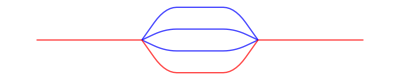

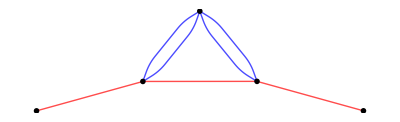
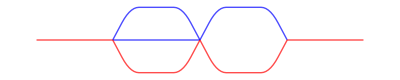
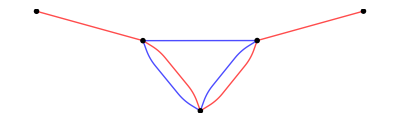
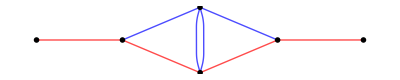
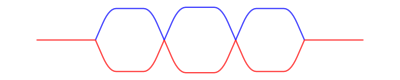
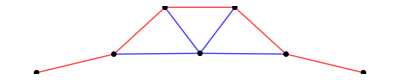
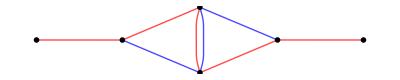
{-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-,-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-,-Graphics-}

```mathematica
jGraphPlot/@Flatten[MIs/@{HQET1,HQET2,HQET3,HQET4}]
```

```mathematica
DiskSave/@{HQET1,HQET2,HQET3,HQET4};
NotebookSave[]
Quit[]
```

## Ds Set

```mathematica
Get/@{"Bases/HQET1/HQET1","Bases/HQET2/HQET2","Bases/HQET3/HQET3","Bases/HQET4/HQET4"}
```

{Bases/HQET1,Bases/HQET2,Bases/HQET3,Bases/HQET4}

Let us now consider diagram with 5 linear propagators:

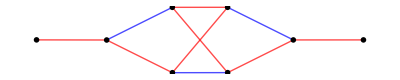

```mathematica
topo={{1->2,1},{2->3,1},{3->4,1},{4->5,1},{5->6,1},{1->4,0},{2->5,0},{3->6,0},{-1->1,1,0},{6->-6,1,0}};
FeynGraphPlot[topo]
```

```mathematica
NewDsSet[HQET5,GraphToDs[topo,{l1,l2,l3},Switch[#1,1,1-2sp[#2,v],0,-sp[#2]]&],{l1,l2,l3},Append->True,FindExtSymmetries->{HQET4,HQET3,HQET2,HQET1},GeneratePFGB->True,Directory->"Bases/HQET5"];
```

Irreducible numerator(s) appended: l1·l2,l1·l3,l2·l3.
Using {___,0, 0, 0} as a pattern for AnalyzeSectors.

Generating Groebner basis for partial fractioning…

Found relations
    1 - d2 + d3 - d5 == 0
    1 - d1 + d3 - d4 == 0

Groebner basis for partial fractioning is generated.
    PFGB[HQET5] — a list  (wrapped in HoldForm) {denominators,numerators,basis,ordermatrix}.

Analyzing sectors…

Found 232(24) zero(nonzero) sectors out of 256.
    ZeroSectors[HQET5] — zero sectors,
    NonZeroSectors[HQET5] — nonzero sectors,
    SimpleSectors[HQET5] — simple sectors (no nonzero subsectors),
    BasisSectors[HQET5] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[HQET5] — a rule to nullify all zero j[HQET5…],
    CutDs[HQET5] — a flag list of cut denominators (1=cut).

The directory Bases/HQET5 has been created.

Finding external symmetries…

Found 12 sectors mapped onto HQET1.
    ExtUniqueSectors[HQET5] — new sectors of the basis.
    ExtMappedSectors[HQET5] — a list of mapped sectors.
    jExtRules[HQET5,…] — reduction rules for j[HQET5,…] from ExtMappedSectors[HQET5].
    ExtSectorsMappings[HQET5] — gives the list of mappings of all sectors from ExtMappedSectors[HQET5] to unique sectors of other bases.

Found 4 sectors mapped onto HQET2.
    ExtUniqueSectors[HQET5] — new sectors of the basis.
    ExtMappedSectors[HQET5] — a list of mapped sectors.
    jExtRules[HQET5,…] — reduction rules for j[HQET5,…] from ExtMappedSectors[HQET5].
    ExtSectorsMappings[HQET5] — gives the list of mappings of all sectors from ExtMappedSectors[HQET5] to unique sectors of other bases.

Found 0 sectors mapped onto HQET3.
    ExtUniqueSectors[HQET5] — new sectors of the basis.
    ExtMappedSectors[HQET5] — a list of mapped sectors.
    jExtRules[HQET5,…] — reduction rules for j[HQET5,…] from ExtMappedSectors[HQET5].
    ExtSectorsMappings[HQET5] — gives the list of mappings of all sectors from ExtMappedSectors[HQET5] to unique sectors of other bases.

Found 0 sectors mapped onto HQET4.
    ExtUniqueSectors[HQET5] — new sectors of the basis.
    ExtMappedSectors[HQET5] — a list of mapped sectors.
    jExtRules[HQET5,…] — reduction rules for j[HQET5,…] from ExtMappedSectors[HQET5].
    ExtSectorsMappings[HQET5] — gives the list of mappings of all sectors from ExtMappedSectors[HQET5] to unique sectors of other bases.

Valid set.
    Ds[HQET5] — denominators,
    SPs[HQET5] — scalar products involving loop momenta,
    LMs[HQET5] — loop momenta,
    EMs[HQET5] — external momenta,
    Relations[HQET5] — relations between denominators.
The definitions of the set will be saved in Bases/HQET5

```mathematica
DiskSave[HQET5]
NotebookSave[]
Quit[]
```

## Reduction

```mathematica
Get/@{"Bases/HQET1/HQET1","Bases/HQET2/HQET2","Bases/HQET3/HQET3","Bases/HQET4/HQET4","Bases/HQET5/HQET5"}
```

{Bases/HQET1,Bases/HQET2,Bases/HQET3,Bases/HQET4,Bases/HQET5}

Using IBPReduce solely will not reduce integrals with linearly dependent denominators:

```mathematica
IBPReduce[j[HQET5,1,2,1,1,1,2,1,1,-1,-1,0]]
```

j[HQET5,1,2,1,1,1,2,1,1,-1,-1,0]

We have to PFReduce such integrals first:

```mathematica
tmp=PFReduce[j[HQET5,1,2,1,3,1,2,1,1,-1,-1,-1]]
```

j[HQET5,0,0,1,1,1,2,1,1,-1,-1,-1]+j[HQET5,0,0,1,2,1,2,1,1,-1,-1,-1]+j[HQET5,0,0,1,3,1,2,1,1,-1,-1,-1]-j[HQET5,0,1,0,1,1,2,1,1,-1,-1,-1]+j[HQET5,0,1,0,1,3,2,1,1,-1,-1,-1]+2 j[HQET5,0,1,0,1,4,2,1,1,-1,-1,-1]+3 j[HQET5,0,1,0,1,5,2,1,1,-1,-1,-1]-j[HQET5,0,1,0,2,1,2,1,1,-1,-1,-1]+j[HQET5,0,1,0,2,3,2,1,1,-1,-1,-1]+2 j[HQET5,0,1,0,2,4,2,1,1,-1,-1,-1]-j[HQET5,0,1,0,3,1,2,1,1,-1,-1,-1]+j[HQET5,0,1,0,3,3,2,1,1,-1,-1,-1]+j[HQET5,0,1,1,1,0,2,1,1,-1,-1,-1]+j[HQET5,0,1,1,2,0,2,1,1,-1,-1,-1]+j[HQET5,0,1,1,3,0,2,1,1,-1,-1,-1]-j[HQET5,0,2,0,1,1,2,1,1,-1,-1,-1]-j[HQET5,0,2,0,1,2,2,1,1,-1,-1,-1]-j[HQET5,0,2,0,1,3,2,1,1,-1,-1,-1]-j[HQET5,0,2,0,1,4,2,1,1,-1,-1,-1]-j[HQET5,0,2,0,2,1,2,1,1,-1,-1,-1]-j[HQET5,0,2,0,2,2,2,1,1,-1,-1,-1]-j[HQET5,0,2,0,2,3,2,1,1,-1,-1,-1]-j[HQET5,0,2,0,3,1,2,1,1,-1,-1,-1]-j[HQET5,0,2,0,3,2,2,1,1,-1,-1,-1]+j[HQET5,0,2,1,1,0,2,1,1,-1,-1,-1]+j[HQET5,0,2,1,2,0,2,1,1,-1,-1,-1]+j[HQET5,0,2,1,3,0,2,1,1,-1,-1,-1]-j[HQET5,1,0,0,1,3,2,1,1,-1,-1,-1]-2 j[HQET5,1,0,0,1,4,2,1,1,-1,-1,-1]-3 j[HQET5,1,0,0,1,5,2,1,1,-1,-1,-1]-j[HQET5,1,0,0,2,3,2,1,1,-1,-1,-1]-2 j[HQET5,1,0,0,2,4,2,1,1,-1,-1,-1]-j[HQET5,1,0,0,3,3,2,1,1,-1,-1,-1]+j[HQET5,1,0,1,0,1,2,1,1,-1,-1,-1]-j[HQET5,1,1,0,0,1,2,1,1,-1,-1,-1]+j[HQET5,1,1,0,0,3,2,1,1,-1,-1,-1]+2 j[HQET5,1,1,0,0,4,2,1,1,-1,-1,-1]+3 j[HQET5,1,1,0,0,5,2,1,1,-1,-1,-1]+j[HQET5,1,1,1,0,0,2,1,1,-1,-1,-1]-j[HQET5,1,2,0,0,1,2,1,1,-1,-1,-1]-j[HQET5,1,2,0,0,2,2,1,1,-1,-1,-1]-j[HQET5,1,2,0,0,3,2,1,1,-1,-1,-1]-j[HQET5,1,2,0,0,4,2,1,1,-1,-1,-1]+j[HQET5,1,2,1,0,0,2,1,1,-1,-1,-1]

```mathematica
IBPReduce[tmp]
```

((568960-1796720 d+2449512 d^2-1866067 d^3+868418 d^4-254031 d^5+45984 d^6-4752 d^7+216 d^8) j[HQET1,0,0,1,1,1,0,1,0,0])/(64 (-5+d) (-4+d)^2 (-3+d)^2 (-1+d) (-5+2 d))+((714000-3813568 d+5958098 d^2-4684913 d^3+2195516 d^4-653816 d^5+125038 d^6-14835 d^7+988 d^8-28 d^9) j[HQET1,0,1,1,1,1,0,0,1,0])/(64 (-7+d) (-6+d) (-5+d) (-4+d) (-3+d) (-1+d))+(3 (-10886400+42755296 d-78686208 d^2+85019608 d^3-59204160 d^4+27912958 d^5-9114377 d^6+2063643 d^7-317260 d^8+31458 d^9-1803 d^10+45 d^11) j[HQET1,1,0,1,0,1,1,1,0,0])/(256 (-7+d) (-6+d) (-5+d) (-4+d) (-3+d) (-1+d) (-7+2 d))+((-4-9 d) j[HQET2,1,1,1,1,0,1,0,1,0])/(32 (-1+d))